```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
WPM=40;WPL=30;WPP=15;
(**)
```

```mathematica
q = 51; V0=(204/100)*10^(-8);
t0 = (q*(3*q-1)/V0)^(1/2);ϕ0=1; dϕ0=N[(((2*q)^(1/2))/t0),60];Ni=0;Nf=70;
```

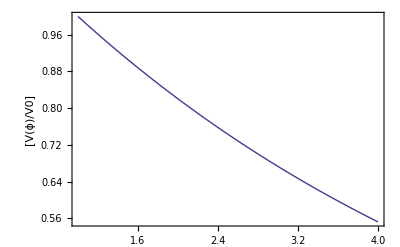

```mathematica
V[ϕ_] = V0*Exp[-((2/q)^(1/2))*(ϕ-ϕ0)];
DV[ϕ_] = D[V[ϕ],ϕ];
Plot[(V[ϕ]/V0),{ϕ,ϕ0,4},PlotRange->All,Frame->True, FrameLabel->{"[V(ϕ)/V0]"}]
```

```mathematica
H0 = ((1/3)*((dϕ0^2/2)+V[ϕ0]))^(1/2);
Dϕ0 = (dϕ0/H0);
```

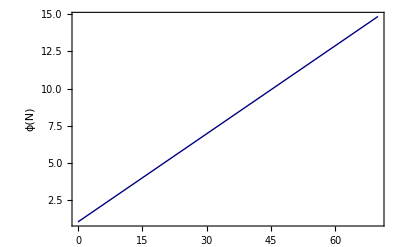

```mathematica
ϕSoln=NDSolve[{ϕ''[N]+(3-ϕ'[N]^2/2)*ϕ'[N]+(DV[ϕ[N]]/(2*V[ϕ[N]]))*(6-(ϕ'[N])^2)==0,ϕ[Ni]==ϕ0,ϕ'[Ni]==Dϕ0},ϕ,{N,Ni,Nf},MaxSteps->1000000, WorkingPrecision->WPM];
ϕ[N_]=ϕ[N]/.Flatten[ϕSoln];
Plot[ϕ[N],{N,Ni,Nf},Frame->True,PlotRange->All,FrameLabel->{"ϕ(N)"},PlotStyle->{Darker[Blue,0.5]}]
```

```mathematica
toFile = Table[{" ",N[N,10] ,N[ϕ[N],10] ," "},{N,Ni,Nf,(Nf-Ni)/10}]//N
Export["~/Github/project_work/small_field/phi_vs_N_mathematica.txt",toFile];
```

{{ ,0.[0.,10.],0.[1.,10.], },{ ,7.[7.,10.],7.[2.38621,10.], },{ ,14.[14.,10.],14.[3.77241,10.], },{ ,21.[21.,10.],21.[5.15862,10.], },{ ,28.[28.,10.],28.[6.54483,10.], },{ ,35.[35.,10.],35.[7.93103,10.], },{ ,42.[42.,10.],42.[9.31724,10.], },{ ,49.[49.,10.],49.[10.7034,10.], },{ ,56.[56.,10.],56.[12.0897,10.], },{ ,63.[63.,10.],63.[13.4759,10.], },{ ,70.[70.,10.],70.[14.8621,10.], }}

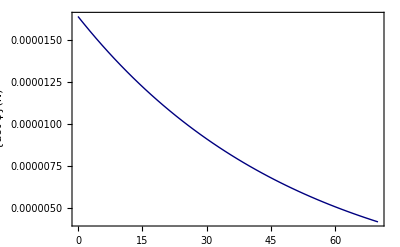

```mathematica
H[N_]=(V[ϕ[N]]/(3-((ϕ'[N])^2)/2))^(1/2);
Plot[{H[N]*ϕ'[N]},{N,Ni,Nf},Frame->True, PlotRange->All, FrameLabel->{"{dot ϕ}(N)"},PlotStyle->{Darker
[Blue,0.5]}]
```

```mathematica
toFile =Table[{" ",N[N,10],N[H[N],10]," "},{N,Ni,Nf,(Nf-Ni)/10}]//N;
Export["~/Github/project_work/small_field/H_vs_N_mathematica.txt",toFile];
```

```mathematica
toFile = Table[{" ",N[N,10],N[H'[N]*10^6,10]," "},{N,Ni,Nf,(Nf-Ni)/10}]//N;
Export["~/Github/project_work/small_field/DH_vs_N_mathematica.txt",toFile];
```

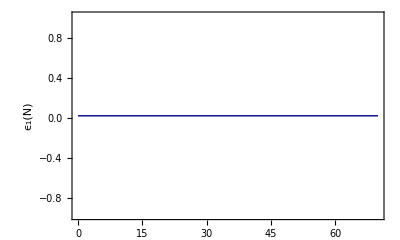

```mathematica
ϵ1[N_] =((ϕ'[N])^2/2);
Plot[ϵ1[N],{N,Ni,Nf},Frame->True, PlotRange->All, AspectRatio->0.6,FrameLabel->{"\!\(\*SubscriptBox[\(ϵ\),\(1\)]\)(N)"},PlotStyle->{Darker[Blue, 0.5]}]
```

```mathematica
toFile=Table[{" ",N[N,10],N[ϵ1[N],10]," "},{N,Ni,Nf,(Nf-Ni)/10}]//N;
Export["~/Github/project_work/small_field/eps_vs_N_mathematica.txt",toFile];
```

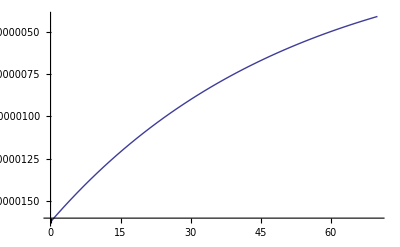

```mathematica
Plot[H'[N],{N,Ni,Nf}]
```

```mathematica
ai = 10^(-5);
A[N_] = ai*Exp[N]
```

ⅇ^N/100000

```mathematica
k = 10^(-6)
N[k]
Nics=N/.FindRoot[k==(10^2*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL]
N[Nics]
```

1/1000000

1.×10^-6

2.54198038578949765072641948787

2.54198

```mathematica
toFile = Table[{k = 10^(y);N[k,10],
Nics=N/.FindRoot[k==(10^2*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL];N[Nics],
Nshss=N/.FindRoot[k==(10^(-3)*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL];N[Nshss],
hkSoln = NDSolve[{hk''[N1]+hk'[N1]*(H'[N1]/H[N1]+3)+hk[N1]*(k/(H[N1]*A[N1]))^2==0, hk[Nics]==1/((k)^(1/2)*A[Nics]),hk'[Nics]==-I*(k)^(1/2)/(A[Nics]^2*H[Nics])-1/(A[Nics]*(k)^(1/2))},hk,{N1,Nics,Nshss}, InterpolationOrder->All,MaxSteps->10000000, WorkingPrecision->WPP];
N[4*(k^3/(2*Pi^2))*(Abs[hk[Nshss]/.Flatten[hkSoln]]^2)]*10^(10)},{y,-(60/10),-(0/10),1/2}]
```

{{1.×10^-6,2.54198,14.2852,10.3287},{3.16227766×10^-6,3.7163,15.4595,9.86387},{0.00001,4.89062,16.6338,9.41992},{0.0000316227766,6.06494,17.8081,8.99596},{0.0001,7.23925,18.9824,8.59107},{0.000316227766,8.41357,20.1568,8.20441},{0.001,9.58789,21.3311,7.83515},{0.00316227766,10.7622,22.5054,7.48251},{0.01,11.9365,23.6797,7.14575},{0.0316227766,13.1108,24.854,6.82413},{0.1,14.2852,26.0283,6.51703},{0.316227766,15.4595,27.2027,6.22367},{1.,16.6338,28.377,5.94331}}

```mathematica
Export["~/Github/project_work/small_field/tps_mathematica.txt",toFile]
```

~/Github/project_work/small_field/tps_mathematica.txt

```mathematica
(*Table[{k=10^y,
Nics=N/.FindRoot[k==(10^2*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL],
Nshss=N/.FindRoot[k==(10^(-3)*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL],hkSoln = NDSolve[{hk''[N1]+hk'[N1]*(H'[N1]/H[N1]+3)+hk[N1]*(k/(H[N1]*A[N1]))^2==0, hk[Nics]==1/((2*k)^(1/2)*A[Nics]),hk'[Nics]==-I*(k/2)^(1/2)/(A[Nics]^2*H[Nics])-1/(A[Nics]*(2*k)^(1/2))},hk,{N1,Nics,Nshss}, InterpolationOrder->All,MaxSteps->10000000, WorkingPrecision->WPP];
hk[N_]=hk[N]/.hkSoln;N[2*(k^3/(2*Pi^2))*(Abs[hk[Nshss]]^2)]},{y,-6,-5,1/2}]*)
```

```mathematica
(*y = -6
k=10^(y)
Nics=N/.FindRoot[k==(10^2*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL]
Nshss=N/.FindRoot[k==(10^(-3)*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL]*)
```

```mathematica
(*Table[{k=10^y,Nics=N/.FindRoot[k==(10^2*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL],
Nshss=N/.FindRoot[k==(10^(-3)*A[N]*H[N]),{N,Ni,Nf},WorkingPrecision->WPL],hkSoln = NDSolve[{hk''[N1]+hk'[N1]*(H'[N1]/H[N1]+3)+hk[N1]*(k/(H[N1]*A[N1]))^2==0, hk[Nics]==1/((2*k)^(1/2)*A[Nics]),hk'[Nics]==-I*(k/2)^(1/2)/(A[Nics]^2*H[Nics])-1/(A[Nics]*(2*k)^(1/2))},hk,{N1,Nics,Nshss}, InterpolationOrder->All,MaxSteps->10000000];},{y,-6,-5,1/2}]*)
```